```mathematica
Get["lions.mx"];
Get["tigers.mx"];
Get["bears.mx"];
```

```mathematica
data=RandomSample@Flatten[{
Map[#->"lion"&,lions],
Map[#->"tiger"&,tigers],
Map[#->"bear"&,bears]
}];
```

```mathematica
Length[data]
```

2400

```mathematica
training=Take[data,2200];
validation=Take[data,-200];
```

```mathematica
RandomSample[training,5]
```

{-Graphics-→tiger,-Graphics-→bear,-Graphics-→tiger,-Graphics-→tiger,-Graphics-→bear}

```mathematica
Clear[net];
net=NetGraph[<|
"convolve1"->ConvolutionLayer[20,5],
"ramp1"->ElementwiseLayer[Ramp],
"pool1"->PoolingLayer[6,8],
"flatten"->FlattenLayer[],
"connect"->DotPlusLayer[3],
"softmax"->SoftmaxLayer[]
|>,
{"convolve1"->"ramp1"->"pool1"->"flatten"->"connect"->"softmax"},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"lion","tiger","bear"}}]]
```

NetGraph[]

```mathematica
result=NetTrain[net,training,ValidationSet->validation,TargetDevice->"GPU",MaxTrainingRounds->300];
```

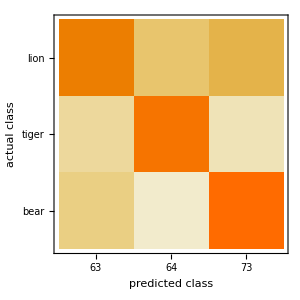
{0.79,-Graphics-}

```mathematica
cm=ClassifierMeasurements[result,validation];
{cm["Accuracy"],cm["ConfusionMatrixPlot"]}
```

```mathematica
conv=NetExtract[result,1]
```

None

```mathematica
RandomSample[validation,3]
```

{-Graphics-→lion,-Graphics-→lion,-Graphics-→tiger}

```mathematica
Image/@Rescale/@conv[NetEncoder[{"Image",{100,100}}][-Graphics-]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image/@Rescale/@conv[NetEncoder[{"Image",{100,100}}][-Graphics-]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image/@Rescale/@conv[NetEncoder[{"Image",{100,100}}][-Graphics-]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}